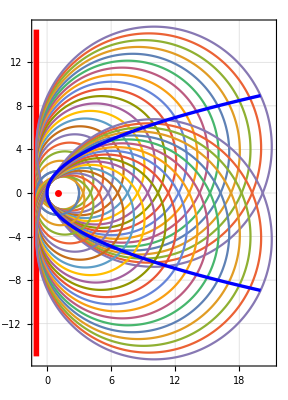

```mathematica
(*Kodutöö NR 3
Siim Erik Pugal
179411YAFB*)
(*parabool, XY ja F*)
funkt=y^2-2 p x;
XY={x,Sqrt[2 p x]};
F={p/2,0};
(*X ja Y muut*) 
muut=XY-F;
sirge={x->XY[[1]]+t muut[[1]],y->XY[[2]]+t muut[[2]]};
(*t avaldatud x ja y vaart*)
tvaart = Solve[(funkt/.sirge)==0,t];
(*Avaldatud x ja y*)
tv=Simplify[sirge/.tvaart[[2]]];
(*Ainult x ja y väärtused*)
XU={x,y}/.tv;
(*Keskpunkt K*)
K=Mean[{XY,XU}];
(*Raadiuse pikkus*)
R=Simplify[Sqrt[(XY[[1]]-K[[1]])^2+(XY[[2]]-K[[2]])^2]];
(*K-s x asendatud λ-ga*)
Kasen=K/.x->λ;
(*R-s x asendatud λ-ga*)
Rasen=R/.x->λ;
(* Parve võrrand *)
parvor=(x-Kasen[[1]])^2+(y-Kasen[[2]])^2-Rasen^2;
(* Tuletis parve võrrandist λ järgi *)
dparvor=D[parvor,λ];
mahised = Solve[Eliminate[{dparvor==0,parvor==0},λ],x];
mahis=mahised[[1]];
(*Sisestan p ja x väärtused*)
(* Uus keskkoht *)
KU=K/.{p->2,x->λ} ;
(* Uus raadius *)
RU=R/.{p->2,x->λ};
(* Ringide valemid *)
ylemised=Table[{KU[[1]]+RU Cos[t],KU[[2]]+RU Sin[t]},{λ,1,20}];
alumised=Table[{KU[[1]]+RU Cos[t],-KU[[2]]+RU Sin[t]},{λ,1,20}];
(* Ringide ja parabooli graafikud *)
ringid1=ParametricPlot[ylemised,{t,0,2 Pi}];(*ringid*)
ringid2=ParametricPlot[alumised,{t,0,2 Pi}];(*ringid*)
parabool=ParametricPlot[{{t,2 Sqrt[t]},{t,-2 Sqrt[t]}},{t,0,20},PlotStyle->{{Blue, Thickness[0.006]}}];
punktid=Table[{x /.mahis[[1]] /. p->2 ,i},{i,-15,15}];
mahisjoon=ListLinePlot[punktid,PlotStyle->{Red,Thickness[0.01]}];
fookus=Graphics[{AbsolutePointSize[5],Red,Point[{1,0}]}];
Show[fookus,mahisjoon,ringid1,ringid2,parabool,AspectRatio->Automatic,PlotRange->Automatic,Axes-> True,GridLines-> Automatic,Frame-> True]
```